```mathematica
dirStr = NotebookDirectory[]~StringJoin~"Utils.nb";

NotebookEvaluate[dirStr];
```

```mathematica
(*We specify the Hamiltonian in pieces*)
(*term1 = p[1]^2/(2m) + 1/2 m ω[1]^2 q[1]^2 + p[2]^2/(2m) + 1/2 m ω[2]^2 q[2]^2;
term2 = λ3[1] q[1]^2 q[2] /3! + λ3[2] q[1] q[2]^2 /3!;
term3 = g4[1] q[1]^4 /4! + g4[2] q[2]^4 /4! + λ4 q[1]^2 q[2]^2 /4!;*)

term1 = p[1]^2/(2m) + 1/2 m ω[1]^2 q[1]^2 + p[2]^2/(2m) + 1/2 m ω[2]^2 q[2]^2 + p[3]^2/(2m) + 1/2 m ω[3]^2 q[3]^2;
term2 = 0;
term3 = g4[1] q[1]^4 /4! + g4[2] q[2]^4 /4! + g4[3] q[3]^4 /4! + λ4[1, 2] q[1]^2 q[2]^2 /4! + + λ4[1, 3] q[1]^2 q[3]^2 /4!;

(*λ3[1] = 0;
λ3[2] = 0;
g4[1] = 0;
g4[2] = 0;
λ4 = 0;*)

eigs = {ω[1], ω[2], ω[3]};
prs = {{p[1], q[1]}, {p[2], q[2]}, {p[3], q[3]}};

(*Some symplectic transformations used below. x' = (x - I p)/√2 = Sqrt[ℏ] a^† (the raising operator).
Similarly, p' = (p - I x)/√2 = -I Sqrt[ℏ] a (lowering operator).*)
scaleRule = {q[1] -> q[1]/Sqrt[m ω[1]],
			p[1] -> Sqrt[m ω[1]]p[1],
			q[2] -> q[2]/Sqrt[m ω[2]],
			p[2] -> Sqrt[m ω[2]]p[2],
			q[3] -> q[3]/Sqrt[m ω[3]],
			p[3] -> Sqrt[m ω[3]]p[3]};
diagRule = {q[1] -> 1/Sqrt[2](q[1] + I p[1]),
			p[1] -> 1/Sqrt[2](p[1] + I q[1]),
			q[2] -> 1/Sqrt[2](q[2] + I p[2]),
			p[2] -> 1/Sqrt[2](p[2] + I q[2]),
			q[3] -> 1/Sqrt[2](q[3] + I p[3]),
			p[3] -> 1/Sqrt[2](p[3] + I q[3])};

(*Choose degeneracy:*)
(*Ω = ω;*)

(*We rescale and diagonalize the Hamiltonian, what we obtain we assign to H[n, m].
Here, n is the order of the term and m is the order of the QNF, which starts at 2.*)
H[0, 2] = 0;
H[1, 2] = 0;
H[2, 2] = Expand[term1 /. scaleRule /. diagRule];
H[3, 2] = Expand[term2 /. scaleRule /. diagRule];
H[4, 2] = Expand[term3 /. scaleRule /. diagRule];
H[n_ ? (# > 4 &), 2] := 0;

H[2, 2]
H[3, 2]
H[4, 2]

QNFOrd = 8;
QNFSymb = computeQNFSymbUpToOrder[QNFOrd]

Table[{k - 1, MB[QNFSymb[[3]], QNFSymb[[k]]]}, {k, 5, Length[QNFSymb], 2}]
```

ⅈ p[1] q[1] ω[1]+ⅈ p[2] q[2] ω[2]+ⅈ p[3] q[3] ω[3]

0

(g4[1] p[1]^4)/(96 m^2 ω[1]^2)-(ⅈ g4[1] p[1]^3 q[1])/(24 m^2 ω[1]^2)-(g4[1] p[1]^2 q[1]^2)/(16 m^2 ω[1]^2)+(ⅈ g4[1] p[1] q[1]^3)/(24 m^2 ω[1]^2)+(g4[1] q[1]^4)/(96 m^2 ω[1]^2)+(g4[2] p[2]^4)/(96 m^2 ω[2]^2)-(ⅈ g4[2] p[2]^3 q[2])/(24 m^2 ω[2]^2)-(g4[2] p[2]^2 q[2]^2)/(16 m^2 ω[2]^2)+(ⅈ g4[2] p[2] q[2]^3)/(24 m^2 ω[2]^2)+(g4[2] q[2]^4)/(96 m^2 ω[2]^2)+(p[1]^2 p[2]^2 λ4[1,2])/(96 m^2 ω[1] ω[2])-(ⅈ p[1] p[2]^2 q[1] λ4[1,2])/(48 m^2 ω[1] ω[2])-(p[2]^2 q[1]^2 λ4[1,2])/(96 m^2 ω[1] ω[2])-(ⅈ p[1]^2 p[2] q[2] λ4[1,2])/(48 m^2 ω[1] ω[2])-(p[1] p[2] q[1] q[2] λ4[1,2])/(24 m^2 ω[1] ω[2])+(ⅈ p[2] q[1]^2 q[2] λ4[1,2])/(48 m^2 ω[1] ω[2])-(p[1]^2 q[2]^2 λ4[1,2])/(96 m^2 ω[1] ω[2])+(ⅈ p[1] q[1] q[2]^2 λ4[1,2])/(48 m^2 ω[1] ω[2])+(q[1]^2 q[2]^2 λ4[1,2])/(96 m^2 ω[1] ω[2])+(g4[3] p[3]^4)/(96 m^2 ω[3]^2)-(ⅈ g4[3] p[3]^3 q[3])/(24 m^2 ω[3]^2)-(g4[3] p[3]^2 q[3]^2)/(16 m^2 ω[3]^2)+(ⅈ g4[3] p[3] q[3]^3)/(24 m^2 ω[3]^2)+(g4[3] q[3]^4)/(96 m^2 ω[3]^2)+(p[1]^2 p[3]^2 λ4[1,3])/(96 m^2 ω[1] ω[3])-(ⅈ p[1] p[3]^2 q[1] λ4[1,3])/(48 m^2 ω[1] ω[3])-(p[3]^2 q[1]^2 λ4[1,3])/(96 m^2 ω[1] ω[3])-(ⅈ p[1]^2 p[3] q[3] λ4[1,3])/(48 m^2 ω[1] ω[3])-(p[1] p[3] q[1] q[3] λ4[1,3])/(24 m^2 ω[1] ω[3])+(ⅈ p[3] q[1]^2 q[3] λ4[1,3])/(48 m^2 ω[1] ω[3])-(p[1]^2 q[3]^2 λ4[1,3])/(96 m^2 ω[1] ω[3])+(ⅈ p[1] q[1] q[3]^2 λ4[1,3])/(48 m^2 ω[1] ω[3])+(q[1]^2 q[3]^2 λ4[1,3])/(96 m^2 ω[1] ω[3])

{{4,0},{6,0},{8,0}}

```mathematica
(*ClearAll[quant];
quant[m_, n_, {P_, Q_}] := Sum[1/2^n Binomial[n, k1] NonCommutativeMultiply @@ (Table[Q, {k2, 1, k1}]~Join~Table[P, {k2, 1, m}]~Join~Table[Q, {k2, 1, n-k1}]), {k1, 0, n}];
quant[1, 0, {P_, Q_}] := P;
quant[0, 1, {P_, Q_}] := Q;
quant[0, 0, {P_, Q_}] := 1;

ClearAll[coeffToQuant];
coeffToQuant[powVec_] := Module[{prods = {}, length},
	Do[
		prods = Append[prods, quant[powVec[[2k - 1]], powVec[[2k]], prs[[k]]]],
		{k, 1, Length[prs]}
	];
	
	prods = DeleteElements[prods, {1}];
	
	length = Length[prods];
	Return[
		Which[
			length > 1, NonCommutativeMultiply @@ prods,
			length == 1, First @ prods,
			length == 0, 1
		]
	]
];

ClearAll[WignerWeylQuant];
WignerWeylQuant[expr_] := Module[
	{coeffRules = CoefficientRules[expr, Flatten[prs]], coeffs, monoms, quantMonoms, res},
	coeffs = Part[#, 2] & /@ coeffRules;
	monoms = Part[#, 1] & /@ coeffRules;
	quantMonoms = coeffToQuant /@ monoms;
	res = Sum[coeffs[[k]]quantMonoms[[k]], {k, 1, Length[coeffs]}];
	Return[res]
];

QNF = WignerWeylQuant /@ QNFSymb

Needs["NC`"];
Needs["NCAlgebra`"];

SetCommutative[{m, ℏ, g3, λ3, g4, λ4, ω}];
SetNonCommutative[{p, q}];

QNF = NCExpand[QNF]*)
```

```mathematica
(*(*Takes into account that p = -I Sqrt[ℏ] a and q = Sqrt[ℏ] a^†, hence because [a, a^†] = 1: p ** q = q ** p - I ℏ.*)
SetNonCommutative[left, right];
ClearAll[nrmOrdRule];
nrmOrdRule = Table[
	NonCommutativeMultiply[left___, prs[[k, 1]], prs[[k, 2]], right___] ->
	NonCommutativeMultiply[left, prs[[k, 2]], prs[[k, 1]], right] +
	(-I ℏ) NonCommutativeMultiply[left, right],
	{k, 1, Length[prs]}
];

ClearAll[needsReordering];
needsReordering[op1_, op2_] := Position[prs, op1][[1, 1]] > Position[prs, op2][[1, 1]];

ClearAll[commuteRule];
commuteRule = {
	NonCommutativeMultiply[left___, s1_, s2_, right___] /; needsReordering[s1, s2] :>
	NonCommutativeMultiply[left, s2, s1, right]
};

ClearAll[joinedRule];
joinedRule = commuteRule~Join~nrmOrdRule;

QNFNormalOrdered = NCExpand[QNF //. joinedRule]*)
```

```mathematica
(*(*Verifies whether the Hamiltonian is still in NF.*)
commuteNO[expr1_, expr2_] := NCExpand[NCExpand[expr1 ** expr2] //. joinedRule] - NCExpand[NCExpand[expr2 ** expr1] //. joinedRule];

Table[{k - 1, commuteNO[QNFNormalOrdered[[3]], QNFNormalOrdered[[k]]]}, {k, 5, Length[QNFNormalOrdered], 2}]*)
```

```mathematica
(*Module[
	{rule = symbRule[59], ruleInv = symbRuleInv[59], terms, flat},
	flat = Flatten @ (Last /@ rule);
	SetNonCommutative[flat];
	terms = Total[QNFNormalOrdered]/.rule;
	coeffs = NCCoefficientList[terms, flat];
	monoms = NCMonomialList[terms, flat]//.ruleInv;
];

ClearAll[matrixElement, n, m]
matrixElement[mon_] := Module[{pl, pr},
	Do[Subscript[pl, k] = Count[Cases[mon, _, Infinity], prs[[k, 1]]], {k, 1, Length[prs]}];
	Do[Subscript[pr, k] = Count[Cases[mon, _, Infinity], prs[[k, 2]]], {k, 1, Length[prs]}];

	Return[
		(*Product[(Sqrt[ℏ]^Subscript[pr, k] (-I Sqrt[ℏ])^Subscript[pl, k]) Sqrt[(Subscript[m, k]!/(Subscript[m, k]-Subscript[pr, k])!)] Sqrt[(Subscript[n, k]!/(Subscript[n, k]-Subscript[pl, k])!)] KroneckerDelta[(Subscript[m, k]- Subscript[pr, k]) - (Subscript[n, k] - Subscript[pl, k])], {k, 1, Length[prs]}]*)
		Product[(Sqrt[ℏ]^Subscript[pr, k] (-I Sqrt[ℏ])^Subscript[pl, k]) Sqrt[FactorialPower[Subscript[m, k], Subscript[pr, k]]] Sqrt[FactorialPower[Subscript[n, k], Subscript[pl, k]]] KroneckerDelta[(Subscript[m, k]- Subscript[pr, k]) - (Subscript[n, k] - Subscript[pl, k])], {k, 1, Length[prs]}]
	];
]

HamiltonianMatrixElem = Expand[coeffs . (matrixElement /@ monoms)];

rescaleCouplingsRule = {λ3[1] -> 3! λ3[1], λ3[2] -> 3! λ3[2], g4[1] -> 4! g4[1], g4[2] -> 4! g4[2], λ4 -> 4! λ4};
(groundStateEnergy = HamiltonianMatrixElem /. {Subscript[n, _] -> 0, Subscript[m, _] -> 0}) /. rescaleCouplingsRule

(*SetCommutative[kg, s, m];
unitRule = {m-> kg, ℏ -> kg m^2 s^-1, ω[n_] -> s^-1, g4[n_] -> kg m^-2 s^-2, λ4 -> kg m^-2 s^-2};
groundStateEnergy/.{Plus -> List}/.unitRule*)*)
```

```mathematica
With[{rule = symbRule[45], ruleInv = symbRuleInv[45]},
	ClearAll[JRule];
	JRule = Flatten[Table[{prs[[k, 1]] prs[[k, 2]] -> -I Subscript[J, k], prs[[k, 1]]^n_ prs[[k, 2]]^n_ -> (-I)^n Subscript[J, k]^n}, {k, 1, Length[prs]}]] /. rule;
	QNFSymbActions = QNFSymb /. rule //. JRule
]

ClearAll[Op];
Op[J_, n_] := Expand[OverHat[J]Op[J, n-1] + (ℏ/2)^2 (n-1)^2 Op[J, n-2]];
Op[J_, 1] := OverHat[J];
Op[J_, 0] := 1;

ClearAll[opRule];
opRule = {Subscript[J, m_] -> Op[Subscript[J, m], 1], Subscript[J, m_]^n_ :> Op[Subscript[J, m], n]};

QNFActions = QNFSymbActions /. opRule
QNFActions = Expand[QNFActions]

ClearAll[nRule];
nRule = {OverHat[Subscript[J, m_]] -> ℏ(Subscript[n, m] + 1/2)};

QNFExplicitQuantumNumbers = Total[Expand[QNFActions /. nRule]]

(*pickStateRule = {Subscript[n, 1] -> 3, Subscript[n, 2] -> 5};
SetCommutative[n];
testExpr2 = QNFExplicitQuantumNumbers /. pickStateRule
testExpr3 = Expand[HamiltonianMatrixElem /. {Subscript[m, 1] -> Subscript[n, 1], Subscript[m, 2] -> Subscript[n, 2]}] /. pickStateRule
FullSimplify[testExpr2 - testExpr3]*)

rescaleCouplingsRule = {g4[arg_] -> 4! g4[arg], λ4[args__] -> 4! λ4[args]};
(groundStateEnergy = QNFExplicitQuantumNumbers /. Subscript[n, _] -> 0) /. rescaleCouplingsRule

(*SetCommutative[kg, s, m];
unitRule = {m-> kg, ℏ -> kg m^2 s^-1, ω[n_] -> s^-1, g4[n_] -> kg m^-2 s^-2, λ4 -> kg m^-2 s^-2};
groundStateEnergy/.{Plus -> List}/.unitRule*)
```

(333 ℏ^4 g4[1]^3)/(16 m^6 ω[1]^8)-(21 ℏ^3 g4[1]^2)/(8 m^4 ω[1]^5)+(3 ℏ^2 g4[1])/(4 m^2 ω[1]^2)+1/2 ℏ ω[1]+(333 ℏ^4 g4[2]^3)/(16 m^6 ω[2]^8)+(105 ℏ^4 g4[2]^2 λ4[1,2])/(16 m^6 ω[1] ω[2]^7)+(3 ℏ^4 g4[2] λ4[1,2]^2)/(4 m^6 ω[1]^2 ω[2]^6)-(21 ℏ^3 g4[2]^2)/(8 m^4 ω[2]^5)+(3 ℏ^4 g4[2] λ4[1,2]^2)/(4 m^6 ω[1]^3 ω[2]^5)+(ℏ^4 λ4[1,2]^3)/(32 m^6 ω[1]^3 ω[2]^5)+(3 ℏ^4 g4[2] λ4[1,2]^2)/(16 m^6 ω[1]^2 (2 ω[1]-2 ω[2]) ω[2]^5)+(9 ℏ^4 g4[1] g4[2] λ4[1,2])/(4 m^6 ω[1]^4 ω[2]^4)+(3 ℏ^4 λ4[1,2]^3)/(16 m^6 ω[1]^4 ω[2]^4)-(3 ℏ^3 g4[2] λ4[1,2])/(4 m^4 ω[1] ω[2]^4)+(3 ℏ^4 g4[1] λ4[1,2]^2)/(4 m^6 ω[1]^5 ω[2]^3)+(ℏ^4 λ4[1,2]^3)/(32 m^6 ω[1]^5 ω[2]^3)-(ℏ^3 λ4[1,2]^2)/(16 m^4 ω[1]^2 ω[2]^3)+(3 ℏ^2 g4[2])/(4 m^2 ω[2]^2)+(3 ℏ^4 g4[1] λ4[1,2]^2)/(4 m^6 ω[1]^6 ω[2]^2)-(ℏ^3 λ4[1,2]^2)/(16 m^4 ω[1]^3 ω[2]^2)-(3 ℏ^4 g4[1] λ4[1,2]^2)/(16 m^6 ω[1]^5 (2 ω[1]-2 ω[2]) ω[2]^2)+(105 ℏ^4 g4[1]^2 λ4[1,2])/(16 m^6 ω[1]^7 ω[2])-(3 ℏ^3 g4[1] λ4[1,2])/(4 m^4 ω[1]^4 ω[2])+(ℏ^2 λ4[1,2])/(4 m^2 ω[1] ω[2])+1/2 ℏ ω[2]+(9 ℏ^4 g4[2] λ4[1,2]^2)/(4 m^6 ω[1]^2 ω[2]^4 (2 ω[1]+2 ω[2])^2)+(3 ℏ^4 λ4[1,2]^3)/(2 m^6 ω[1]^3 ω[2]^3 (2 ω[1]+2 ω[2])^2)+(9 ℏ^4 g4[1] λ4[1,2]^2)/(4 m^6 ω[1]^4 ω[2]^2 (2 ω[1]+2 ω[2])^2)+(ℏ^3 λ4[1,2]^2)/(2 m^4 ω[1] ω[2]^2 (2 ω[1]+2 ω[2])^2)+(ℏ^3 λ4[1,2]^2)/(2 m^4 ω[1]^2 ω[2] (2 ω[1]+2 ω[2])^2)+(9 ℏ^4 g4[2] λ4[1,2]^2)/(8 m^6 ω[1]^2 ω[2]^5 (2 ω[1]+2 ω[2]))-(3 ℏ^4 g4[2] λ4[1,2]^2)/(8 m^6 ω[1] (2 ω[1]-2 ω[2]) ω[2]^5 (2 ω[1]+2 ω[2]))-(3 ℏ^4 g4[2] λ4[1,2]^2)/(4 m^6 ω[1]^3 ω[2]^4 (2 ω[1]+2 ω[2]))-(3 ℏ^4 g4[2] λ4[1,2]^2)/(8 m^6 ω[1]^2 (2 ω[1]-2 ω[2]) ω[2]^4 (2 ω[1]+2 ω[2]))-(3 ℏ^4 g4[1] λ4[1,2]^2)/(4 m^6 ω[1]^4 ω[2]^3 (2 ω[1]+2 ω[2]))+(9 ℏ^4 g4[1] λ4[1,2]^2)/(8 m^6 ω[1]^5 ω[2]^2 (2 ω[1]+2 ω[2]))-(ℏ^3 λ4[1,2]^2)/(2 m^4 ω[1]^2 ω[2]^2 (2 ω[1]+2 ω[2]))+(3 ℏ^4 g4[1] λ4[1,2]^2)/(8 m^6 ω[1]^4 (2 ω[1]-2 ω[2]) ω[2]^2 (2 ω[1]+2 ω[2]))+(3 ℏ^4 g4[1] λ4[1,2]^2)/(8 m^6 ω[1]^5 (2 ω[1]-2 ω[2]) ω[2] (2 ω[1]+2 ω[2]))+(333 ℏ^4 g4[3]^3)/(16 m^6 ω[3]^8)+(105 ℏ^4 g4[3]^2 λ4[1,3])/(16 m^6 ω[1] ω[3]^7)+(3 ℏ^4 g4[3] λ4[1,3]^2)/(4 m^6 ω[1]^2 ω[3]^6)-(21 ℏ^3 g4[3]^2)/(8 m^4 ω[3]^5)+(3 ℏ^4 g4[3] λ4[1,3]^2)/(4 m^6 ω[1]^3 ω[3]^5)+(ℏ^4 λ4[1,3]^3)/(32 m^6 ω[1]^3 ω[3]^5)+(3 ℏ^4 g4[3] λ4[1,3]^2)/(16 m^6 ω[1]^2 (2 ω[1]-2 ω[3]) ω[3]^5)+(9 ℏ^4 g4[1] g4[3] λ4[1,3])/(4 m^6 ω[1]^4 ω[3]^4)+(3 ℏ^4 λ4[1,3]^3)/(16 m^6 ω[1]^4 ω[3]^4)-(3 ℏ^3 g4[3] λ4[1,3])/(4 m^4 ω[1] ω[3]^4)+(3 ℏ^4 g4[3] λ4[1,2] λ4[1,3])/(8 m^6 ω[1]^3 ω[2] ω[3]^4)+(3 ℏ^4 g4[1] λ4[1,3]^2)/(4 m^6 ω[1]^5 ω[3]^3)+(ℏ^4 λ4[1,3]^3)/(32 m^6 ω[1]^5 ω[3]^3)-(ℏ^3 λ4[1,3]^2)/(16 m^4 ω[1]^2 ω[3]^3)+(ℏ^4 λ4[1,2] λ4[1,3]^2)/(8 m^6 ω[1]^4 ω[2] ω[3]^3)+(3 ℏ^2 g4[3])/(4 m^2 ω[3]^2)+(3 ℏ^4 g4[1] λ4[1,3]^2)/(4 m^6 ω[1]^6 ω[3]^2)-(ℏ^3 λ4[1,3]^2)/(16 m^4 ω[1]^3 ω[3]^2)+(3 ℏ^4 λ4[1,2] λ4[1,3]^2)/(32 m^6 ω[1]^5 ω[2] ω[3]^2)-(3 ℏ^4 g4[1] λ4[1,3]^2)/(16 m^6 ω[1]^5 (2 ω[1]-2 ω[3]) ω[3]^2)+(105 ℏ^4 g4[1]^2 λ4[1,3])/(16 m^6 ω[1]^7 ω[3])-(3 ℏ^3 g4[1] λ4[1,3])/(4 m^4 ω[1]^4 ω[3])+(ℏ^2 λ4[1,3])/(4 m^2 ω[1] ω[3])+(3 ℏ^4 g4[2] λ4[1,2] λ4[1,3])/(8 m^6 ω[1]^3 ω[2]^4 ω[3])+(ℏ^4 λ4[1,2]^2 λ4[1,3])/(8 m^6 ω[1]^4 ω[2]^3 ω[3])+(3 ℏ^4 λ4[1,2]^2 λ4[1,3])/(32 m^6 ω[1]^5 ω[2]^2 ω[3])+(3 ℏ^4 g4[1] λ4[1,2] λ4[1,3])/(2 m^6 ω[1]^6 ω[2] ω[3])-(ℏ^3 λ4[1,2] λ4[1,3])/(8 m^4 ω[1]^3 ω[2] ω[3])+(ℏ^4 λ4[1,2]^2 λ4[1,3])/(4 m^6 ω[1]^3 ω[2]^2 (2 ω[1]+2 ω[2])^2 ω[3])-(ℏ^4 λ4[1,2]^2 λ4[1,3])/(8 m^6 ω[1]^3 ω[2]^3 (2 ω[1]+2 ω[2]) ω[3])+(ℏ^4 λ4[1,2]^2 λ4[1,3])/(8 m^6 ω[1]^4 ω[2]^2 (2 ω[1]+2 ω[2]) ω[3])+1/2 ℏ ω[3]+(9 ℏ^4 g4[3] λ4[1,3]^2)/(4 m^6 ω[1]^2 ω[3]^4 (2 ω[1]+2 ω[3])^2)+(3 ℏ^4 λ4[1,3]^3)/(2 m^6 ω[1]^3 ω[3]^3 (2 ω[1]+2 ω[3])^2)+(9 ℏ^4 g4[1] λ4[1,3]^2)/(4 m^6 ω[1]^4 ω[3]^2 (2 ω[1]+2 ω[3])^2)+(ℏ^3 λ4[1,3]^2)/(2 m^4 ω[1] ω[3]^2 (2 ω[1]+2 ω[3])^2)+(ℏ^4 λ4[1,2] λ4[1,3]^2)/(4 m^6 ω[1]^3 ω[2] ω[3]^2 (2 ω[1]+2 ω[3])^2)+(ℏ^3 λ4[1,3]^2)/(2 m^4 ω[1]^2 ω[3] (2 ω[1]+2 ω[3])^2)+(9 ℏ^4 g4[3] λ4[1,3]^2)/(8 m^6 ω[1]^2 ω[3]^5 (2 ω[1]+2 ω[3]))-(3 ℏ^4 g4[3] λ4[1,3]^2)/(8 m^6 ω[1] (2 ω[1]-2 ω[3]) ω[3]^5 (2 ω[1]+2 ω[3]))-(3 ℏ^4 g4[3] λ4[1,3]^2)/(4 m^6 ω[1]^3 ω[3]^4 (2 ω[1]+2 ω[3]))-(3 ℏ^4 g4[3] λ4[1,3]^2)/(8 m^6 ω[1]^2 (2 ω[1]-2 ω[3]) ω[3]^4 (2 ω[1]+2 ω[3]))-(3 ℏ^4 g4[1] λ4[1,3]^2)/(4 m^6 ω[1]^4 ω[3]^3 (2 ω[1]+2 ω[3]))-(ℏ^4 λ4[1,2] λ4[1,3]^2)/(8 m^6 ω[1]^3 ω[2] ω[3]^3 (2 ω[1]+2 ω[3]))+(9 ℏ^4 g4[1] λ4[1,3]^2)/(8 m^6 ω[1]^5 ω[3]^2 (2 ω[1]+2 ω[3]))-(ℏ^3 λ4[1,3]^2)/(2 m^4 ω[1]^2 ω[3]^2 (2 ω[1]+2 ω[3]))+(ℏ^4 λ4[1,2] λ4[1,3]^2)/(8 m^6 ω[1]^4 ω[2] ω[3]^2 (2 ω[1]+2 ω[3]))+(3 ℏ^4 g4[1] λ4[1,3]^2)/(8 m^6 ω[1]^4 (2 ω[1]-2 ω[3]) ω[3]^2 (2 ω[1]+2 ω[3]))+(3 ℏ^4 g4[1] λ4[1,3]^2)/(8 m^6 ω[1]^5 (2 ω[1]-2 ω[3]) ω[3] (2 ω[1]+2 ω[3]))

```mathematica
(*Δ = 1/Sqrt[15]; (*Irrational difference between the energies, so we have no possible resonance anywhere ever.*)
ϵ = 0.02;
cutOff = 30;
substAllConstsRule = {ω[1] -> 1 + Δ/2, ω[2] -> 1 - Δ/2, m -> 1, λ3[1] -> 0, λ3[2] -> 0, g4[1] -> ϵ, g4[2] -> ϵ, λ4 -> ϵ, ℏ -> 1};
substAllConstsFreeRule = {ω[1] -> 1 + Δ/2, ω[2] -> 1 - Δ/2, m -> 1, λ3[1] -> 0, λ3[2] -> 0, g4[1] -> 0, g4[2] -> 0, λ4 -> 0, ℏ -> 1};*)

ϵ = 0.2;
cutOff = 20;
substAllConstsRule = {ω[1] -> N[Sqrt[5]/2], ω[2] -> N[Sqrt[6]/2], ω[3] -> N[Sqrt[7]/2], m -> 1, g4[_] -> ϵ, λ4[__] -> ϵ, ℏ -> 1};
substAllConstsFreeRule = {ω[1] -> N[Sqrt[5]/2], ω[2] -> N[Sqrt[6]/2], ω[3] -> N[Sqrt[7]/2], m -> 1, g4[_] -> 0, λ4[__] -> 0, ℏ -> 1};

ClearAll[truncateRule]
truncateRule[n_] := {ℏ^m_ /; m > n -> 0};

ClearAll[
	energyPerturbed, energyPerturbedList, energyFree,
	elemExprPerturbed, elemExprFree,
	sumListPerturbed, sumListFree
];

elemExprFree = N[QNFExplicitQuantumNumbers /. substAllConstsFreeRule];
(*elemExprFree = N[HamiltonianMatrixElem /. {Subscript[m, k_]-> Subscript[n, k]} /. substAllConstsFreeRule];*) (*Use this if one wants to use the explicit quantization code.*)
energyFree[tuple_] := energyFree[tuple] = elemExprFree /. {Subscript[n, 1] -> tuple[[1]], Subscript[n, 2] -> tuple[[2]], Subscript[n, 3] -> tuple[[3]]};
sumListFree = generateOrderedTuplesUpToThreshold[energyFree, 3, cutOff];

maxOrd = Floor[QNFOrd/2];
Do[
	With[
		{k = k1},
		elemExprPerturbed[k] = N[QNFExplicitQuantumNumbers /. truncateRule[k] /. substAllConstsRule]
		(*elemExprPerturbed[k] = N[HamiltonianMatrixElem /. {Subscript[m, k_]-> Subscript[n, k]} /. truncateRule[k] /. substAllConstsRule]*) (*Use this if one wants to use the explicit quantization code*)
	],
	{k1, 1, maxOrd}
]
energyPerturbedList[tuple_] := energyPerturbedList[tuple] = Table[With[{k = k1}, elemExprPerturbed[k] /. {Subscript[n, 1] -> tuple[[1]], Subscript[n, 2] -> tuple[[2]], Subscript[n, 3] -> tuple[[3]]}], {k1, 1, maxOrd}]
energyPerturbed[tuple_] := findInterval @ energyPerturbedList[tuple]
sumListPerturbed = generateOrderedTuplesUpToThreshold[energyPerturbed[#][[1, 1]] &, 3, cutOff];
```

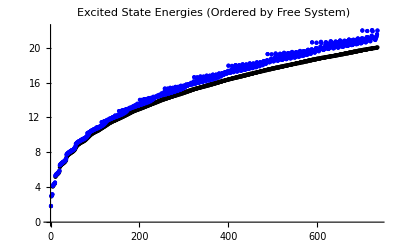

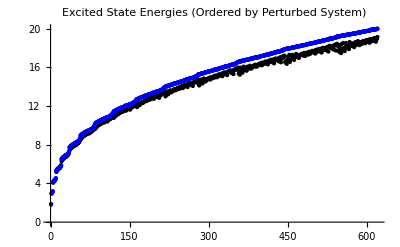

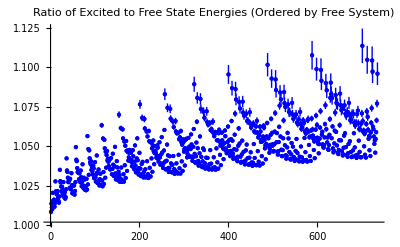

```mathematica
(*############################## Plot 1 ##############################*)
(*####################################################################*)

ClearAll[data1, data2, data1Style, data2Style]

data1 = Table[{k, energyFree[sumListFree[[k]]]}, {k, 1, Length[sumListFree]}];
data2 = {#} & /@ Table[{k, First @ energyPerturbed[sumListFree[[k]]]}, {k, 1, Length[sumListFree]}];
data1Style = {Black, PointSize[Medium]};
data2Style = Table[Last @ energyPerturbed[sumListFree[[k]]] /. {True -> {Blue, PointSize[Medium]}, False -> {Red, PointSize[Medium]}}, {k, 1, Length[sumListFree]}];

ListPlot[
	{data1}~Join~data2,
	ImageSize -> Full,
	PlotStyle -> {data1Style}~Join~data2Style,
	PlotLabel -> "Excited State Energies (Ordered by Free System)"
]

ClearAll[data1, data2, data1Style, data2Style]

(*############################## Plot 2 ##############################*)
(*####################################################################*)

ClearAll[data1, data2, data1Style, data2Style]

data1 = Table[{k, energyFree[sumListPerturbed[[k]]]}, {k, 1, Length[sumListPerturbed]}];
data2 = {#} & /@ Table[{k, First @ energyPerturbed[sumListPerturbed[[k]]]}, {k, 1, Length[sumListPerturbed]}];
data1Style = {Black, PointSize[Medium]};
data2Style = Table[Last @ energyPerturbed[sumListPerturbed[[k]]] /. {True -> {Blue, PointSize[Medium]}, False -> {Red, PointSize[Medium]}}, {k, 1, Length[sumListPerturbed]}];

ListPlot[
	{data1}~Join~data2,
	ImageSize -> Full,
	PlotStyle -> {data1Style}~Join~data2Style,
	PlotLabel -> "Excited State Energies (Ordered by Perturbed System)"
]

ClearAll[data1, data2, data1Style, data2Style]

(*############################## Plot 3 ##############################*)
(*####################################################################*)

ClearAll[data1, data1Style]

data1 = {#} & /@ Table[{k, (First @ energyPerturbed[sumListFree[[k]]])/energyFree[sumListFree[[k]]]}, {k, 1, Length[sumListFree]}];
data1Style = Table[Last @ energyPerturbed[sumListFree[[k]]] /. {True -> {Blue, PointSize[Medium]}, False -> {Red, PointSize[Medium]}}, {k, 1, Length[sumListFree]}];

ListPlot[
	data1,
	ImageSize -> Full,
	PlotStyle -> data1Style,
	PlotLabel -> "Ratio of Excited to Free State Energies (Ordered by Free System)"
]

ClearAll[data1, data1Style]
```

```mathematica
ClearAll[BoltzmannWeightsFree, BoltzmannWeightsPerturbed, Z, β];
BoltzmannWeightsFree[β_] = Exp /@ (-β energyFree[#] & /@ sumListFree);
BoltzmannWeightsPerturbed[β_] = Exp /@ (-β (First @ energyPerturbed[#]) & /@ sumListPerturbed);

Subscript[Z, 0][β_] = Total[BoltzmannWeightsFree[β]];
ZAnalytic[β_] = Product[1 / (2 Sinh[β ℏ ω[k] / 2]), {k, 1, Length[prs]}] /. substAllConstsFreeRule;
Z[β_] = Total[BoltzmannWeightsPerturbed[β]];

Global`Z[β_] = Z[β];
Global`ZAnalytic[β_] = ZAnalytic[β];
Subscript[Global`Z, 0][β_] = Subscript[Z, 0][β];
Global`groundStateEnergyPerturbed = groundStateEnergy /. substAllConstsRule;
Global`groundStateEnergyFree = groundStateEnergy /. substAllConstsFreeRule;
Global`substAllConstsRule = substAllConstsRule;
Global`substAllConstsFreeRule = substAllConstsFreeRule;
```

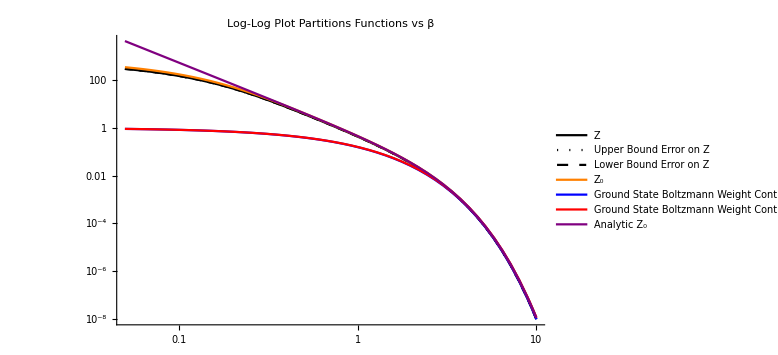

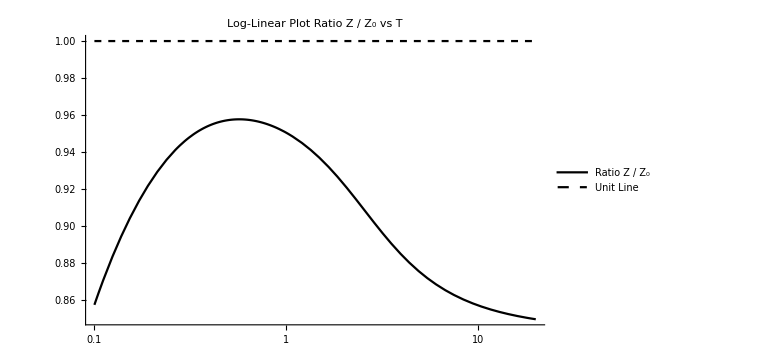

```mathematica
TMin = 0.1;
TMax = cutOff;

LogLogPlot[
	{Evaluate[Z[β] /. {Around[a_, b_]-> a}],
	Evaluate[Z[β] /. {Around[a_, b_]-> a + b}],
	Evaluate[Z[β] /. {Around[a_, b_]-> a - b}],
	Subscript[Z, 0][β],
	Exp[-β N[groundStateEnergy /. substAllConstsRule]],
	Exp[-β N[groundStateEnergy /. substAllConstsFreeRule]],
	ZAnalytic[β]},
	{β, 1/TMax, 1/TMin},
	PlotRange -> Full,
	ImageSize -> Large,
	PlotStyle -> {Black, {Black, Dotted}, {Black, Dashed}, Orange, Blue, Red, Purple},
	PlotLabel -> "Log-Log Plot Partitions Functions vs β",
	PlotLegends -> {
		"Z",
		"Upper Bound Error on Z",
		"Lower Bound Error on Z",
		"Z_0",
		"Ground State Boltzmann Weight Contribution to Z",
		"Ground State Boltzmann Weight Contribution to Z_0",
		"Analytic Z_0"
	}
]

ZRatio[T_] = Z[1/T] / Subscript[Z, 0][1/T];
LogLinearPlot[
	{Evaluate[ZRatio[T] /. {Around[a_, b_]-> a}], 1},
	{T, TMin, TMax},
	PlotRange -> Full,
	ImageSize -> Large,
	PlotStyle -> {Black, {Black, Dashed}},
	PlotLabel -> "Log-Linear Plot Ratio Z / Z_0 vs T",
	PlotLegends -> {"Ratio Z / Z_0", "Unit Line"}
]
```

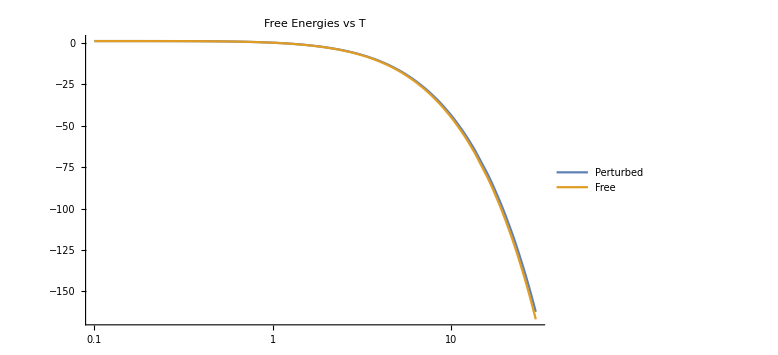

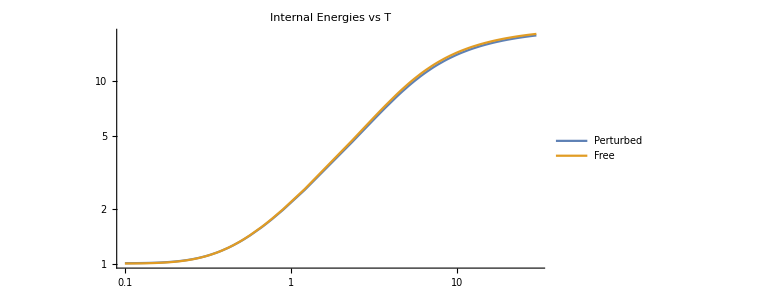

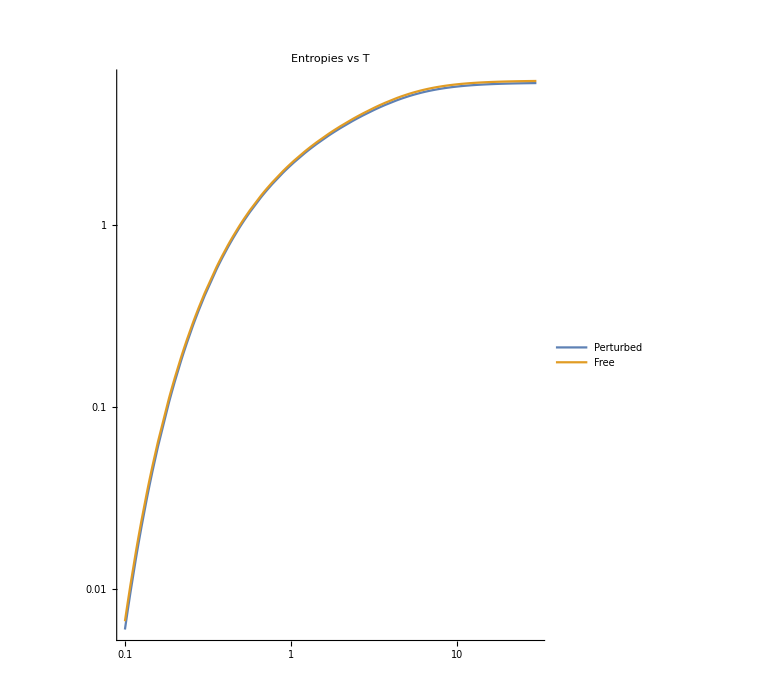

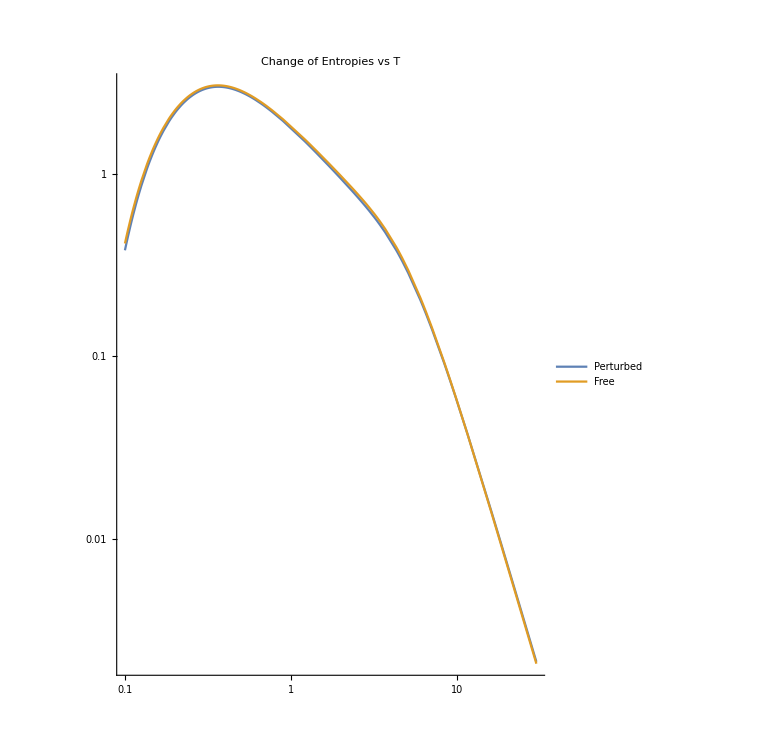

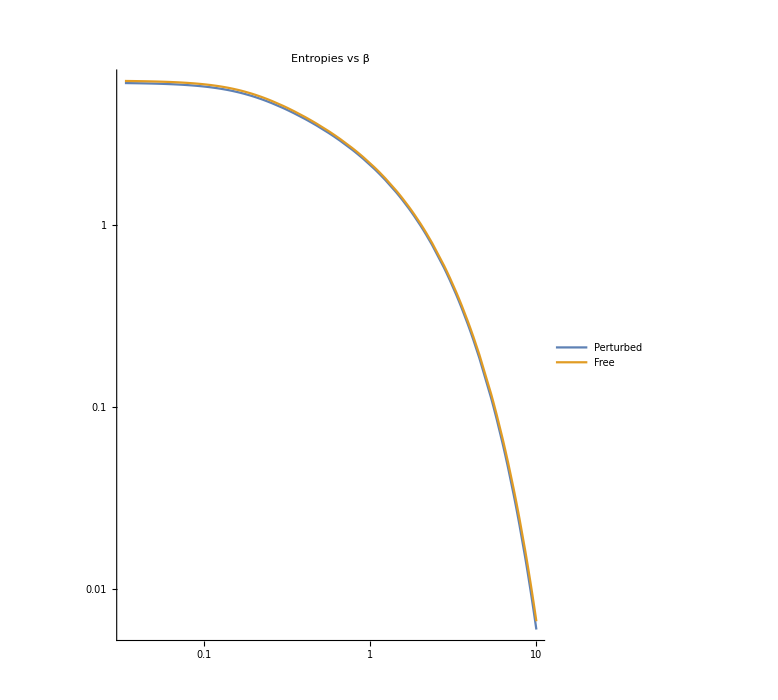

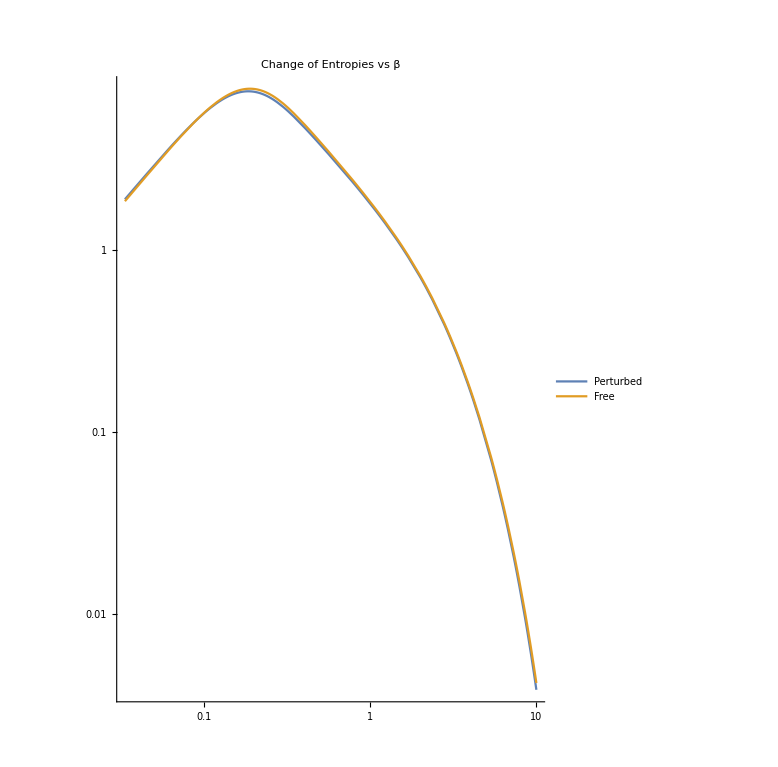

```mathematica
F[β_] = -1/β Log[Z[β]/. {Around[a_, b_]-> a}];
Subscript[F, 0][β_] = -1/β Log[Subscript[Z, 0][β]];

U[β_] = -D[Z[β]/. {Around[a_, b_]-> a}, β]/(Z[β]/. {Around[a_, b_]-> a});
Subscript[U, 0][β_] = -D[Subscript[Z, 0][β], β]/Subscript[Z, 0][β];

S[β_] = Log[Z[β]/. {Around[a_, b_]-> a}] + β U[β];
Subscript[S, 0][β_] = Log[Subscript[Z, 0][β]] + β Subscript[U, 0][β];

DSDT[T_] = D[S[1/T], T];
Subscript[DSDT, 0][T_] = D[Subscript[S, 0][1/T], T];

DSDβ[β_] = D[S[β], β];
Subscript[DSDβ, 0][β_] = D[Subscript[S, 0][β], β];

LogLinearPlot[
	{F[1/T], Subscript[F, 0][1/T]},
	{T, TMin, TMax},
	PlotPoints -> 10,
	PlotRange -> Full,
	ImageSize -> Large,
	PlotLabel -> "Free Energies vs T",
	PlotLegends -> {"Perturbed", "Free"}
]

LogLogPlot[
	{U[1/T], Subscript[U, 0][1/T]},
	{T, TMin, TMax},
	PlotPoints -> 10,
	PlotRange -> Full,
	AspectRatio -> Automatic,
	ImageSize -> Large,
	PlotLabel -> "Internal Energies vs T",
	PlotLegends -> {"Perturbed", "Free"}
]

LogLogPlot[
	{S[1/T], Subscript[S, 0][1/T]},
	{T, TMin, TMax},
	PlotPoints -> 10,
	PlotRange -> Full,
	AspectRatio -> Automatic,
	ImageSize -> Large,
	PlotLabel -> "Entropies vs T",
	PlotLegends -> {"Perturbed", "Free"}
]

LogLogPlot[
	{DSDT[T], Subscript[DSDT, 0][T]},
	{T, TMin, TMax},
	PlotPoints -> 10,
	PlotRange -> Full,
	AspectRatio -> Automatic,
	ImageSize -> Large,
	PlotLabel -> "Change of Entropies vs T",
	PlotLegends -> {"Perturbed", "Free"}
]

LogLogPlot[
	{S[β], Subscript[S, 0][β]},
	{β, 1/TMax, 1/TMin},
	PlotPoints -> 10,
	PlotRange -> Full,
	AspectRatio -> Automatic,
	ImageSize -> Large,
	PlotLabel -> "Entropies vs β",
	PlotLegends -> {"Perturbed", "Free"}
]

LogLogPlot[
	{-DSDβ[β], -Subscript[DSDβ, 0][β]},
	{β, 1/TMax, 1/TMin},
	PlotPoints -> 10,
	PlotRange -> Full,
	AspectRatio -> Automatic,
	ImageSize -> Large,
	PlotLabel -> "Change of Entropies vs β",
	PlotLegends -> {"Perturbed", "Free"}
]
```

```mathematica
Plot[
	{S[β], Subscript[S, 0][β]},
	{β, 1/TMax, 1/TMin},
	PlotPoints -> 10,
	PlotRange -> Full,
	ImageSize -> Large,
	PlotLabel -> "Entropies vs β",
	PlotLegends -> {"Perturbed", "Free"}
]
```

-Graphics-

```mathematica
Plot[
	{S[1/T], Subscript[S, 0][1/T]},
	{T, TMin, TMax},
	PlotPoints -> 10,
	PlotRange -> Full,
	ImageSize -> Large,
	PlotLabel -> "Entropies vs T",
	PlotLegends -> {"Perturbed", "Free"}
]
```

-Graphics-